Curtis Sera
v 3.0
2020-04-21

Protrusion stress and pore expansion

## Calculating protrusion stress

Let' s make our piecewise function for the protrusion membrane surface and graph it as a surface of revolution:

Piecewise[{{500+200 (1-√(1-(200-z)^2/40000)), 0<z≤200}, {500, 200<z≤4500}, {500 √(1-(-4500+z)^2/250000), 4500<z≤5000}, {0, True}}]

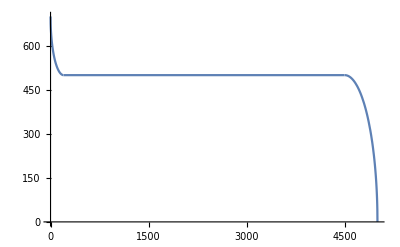

-Graphics3D-

```mathematica
(* System properties/constants *)
R = 500; (* Radius of protrusion's cylindrical body; in nm *)
rt = 200; (*Radius of the torus tube/circle revolved around z for the base; in nm *)
l = 5000; (*Protrusion length; in nm *)

(* Model curvatures *)
κR = 1/R;

κrt=1/rt;
κT[z_] := Sqrt[1-((rt-z)/rt)^2]/(R+rt+rt Sqrt[1-((rt-z)/rt)^2]);(*local radius of curvature for toroidal base*)

(* Piecewise representation of the protrusion surface *)
pwR = Piecewise[{{rt(1-Sqrt[1-((rt-z)/rt)^2])+R,0<z≤rt},
{R,rt<z≤l-R},
{(z-(l-R)) Tan[ArcCos[(z-(l-R))/R]],l-R<z≤ l}}]
Plot[pwR,{z,0,l}]
RevolutionPlot3D[{pwR,z},{z,0,l}] 
	(*Note how we put pwR as "x" and put z last to make it the axis of revolution*)
```

Great!
Now ideally I’d just import the tension data already computed via MATLAB, but I can’t seem to figure out how to use said data to make a color map :\
Instead, we’ll basically just recompute all of that...

0.000560185

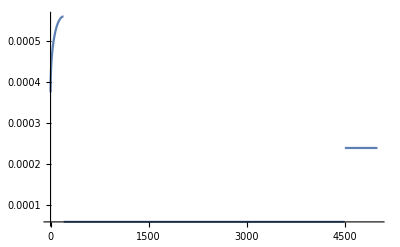

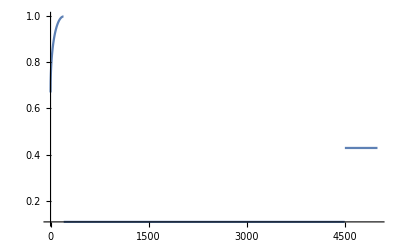

```mathematica
Kbend = 15*2; (* Crudely estimate double-bilayer protrusion's Kb = 2*generic bilayer Kb; in k_B T *)

pwStress[z_]:= Piecewise[{{Kbend*0.5*((κrt+κT[z])^2),0<z≤rt},
{Kbend*0.5*(κR^2),rt<z≤l-R},
{Kbend*2(κR^2),l-R<z≤ l}}]
stressMax=pwStress[rt]
pwStressNorm[z_]:=pwStress[z]/stressMax

Plot[pwStress[z],{z,0,l}]
Plot[pwStressNorm[z],{z,0,l}]
```

Note: We’ve normalized the stress to its maximum to facilitate color mapping
Next, we' ll re - graph our surface using above piecewise function as the coloring guide

```mathematica
tension3dPlot=RevolutionPlot3D[{pwR,z},{z,0,l},
ColorFunction->Function[{x,y,z},
Hue[2(1-pwStressNorm[z])/3]],ColorFunctionScaling->False]
```

-Graphics3D-

Notes on Hue[]: 
- Defined the function such that red is the max and blue is the min 
- To make red correspond to the highest tension, we’ve inverted the scale via 1-pwTension[z]
- To fix the default scheme’s color weirdness (they have magenta/violet as the min which looks a lot like the max’s red), we’ve done 2/3 to basically cut out the magenta